```mathematica
differenze[μ_,x0_,δ_,Ν_]:=Abs[fnList[μ,x0,Ν]-fnList[μ,x0+δ,Ν]]
```

```mathematica
a=Table[{μ,Log@differenze[μ,0.4,2$MachineEpsilon,120]},{μ,3.57,4,10^-3}];
```

```mathematica
b=Association@@({#⟦1⟧,D[Normal[LinearModelFit[DeleteCases[{Range[0,120],#⟦2⟧}ᵀ,{_,Indeterminate}],x,x]], x]}&/@a)/.{List->Rule};
```

```mathematica
b[3.7]
```

0.302519

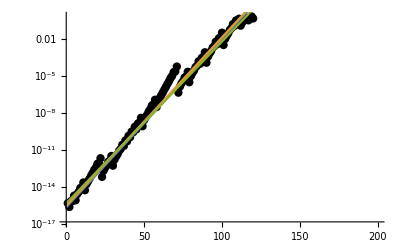

```mathematica
Show[ListLogPlot[Abs[Drop[fnList[3.7,0.4,120]-fnList[3.7,0.4+2$MachineEpsilon,120],-1]],],Plot[{-36.10749693228221+0.3148509107115752 x,-35.79264602157062+0.3148509107115753 x,-35.350631844973904+0.3025194668941214 x},{x,0,120}]]
```

```mathematica
Fit[a[[131,2]],{1,x},x]
```

-35.6532+0.302519 x

```mathematica
-0.0007179766383085418+0.000022451894223379893 x
```

```mathematica
-35.79264602157062+0.3148509107115753 x
```